Copyright (c) 2021 Jason Pereira jason.pereira@york.ac.uk

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the “Software”), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions:

The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM,
OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE.

```mathematica
Clear["Global`*"]
```

```mathematica
(*Define functions to calculate the fidelity and the channel output.*)
Fidelity[rho1_,rho2_]:=Tr[MatrixPower[MatrixPower[rho1,1/2].rho2.MatrixPower[rho1,1/2],1/2]]
PartialTranspose[V_]:=ArrayFlatten[Map[Transpose,Partition[V,{2,2}],{2}]]
TraceMiddleMode[V_]:=V[[{1,2,5,6},{1,2,5,6}]]+V[[{3,4,7,8},{3,4,7,8}]]
LinkProduct[V1_,V2_]:=TraceMiddleMode[KroneckerProduct[IdentityMatrix[2],V1].KroneckerProduct[PartialTranspose[2V2],IdentityMatrix[2]]]
TraceFirstMode[V_]:=V[[{1,2},{1,2}]]+V[[{3,4},{3,4}]]
Rot[r_]:=KroneckerProduct[IdentityMatrix[2],{{Cos[r],Sin[r]},{-Sin[r],Cos[r]}}]

Bell={{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}/2;
(*Choi matrix of a qubit rotation about the X axis*)
RotChoi[r_]:=FullSimplify[Rot[r].Bell.ConjugateTranspose[Rot[r]],Element[r,Reals]]
(*Choi matrix of a measurement along the Z axis (number state basis)*)
(*Non-projective for p < 1*)
SquashChoi[p_]:={{1,0,0,1-p},{0,0,0,0},{0,0,0,0},{1-p,0,0,1}}/2
```

```mathematica
(*Choi matrices of the two channels*)
ChoiC1=SquashChoi[1];
ChoiC2=LinkProduct[RotChoi[-2Δθ],LinkProduct[SquashChoi[1],RotChoi[Δθ]]];

conds={Element[Subscript[θ, 1]|Subscript[θ, 2]|Δθ,Reals]};
(*Input states restricted to this form because any pair of states not in the XZ plane give the same output states as another pair in the XZ plane (due to the projective measurement)*)
"Input states 1 and 2 parametrised by θ_1 and θ_2 respectively."
in1={{Cos[Subscript[θ, 1]]},{-Sin[Subscript[θ, 1]]}};
in2={{Cos[Subscript[θ, 2]]},{-Sin[Subscript[θ, 2]]}};
inState1=FullSimplify[KroneckerProduct[in1,ConjugateTranspose[in1]],conds];
inState2=FullSimplify[KroneckerProduct[in2,ConjugateTranspose[in2]],conds];
"Fidelity of input states:"
FullSimplify[Fidelity[inState1,inState2],conds]
"Input fidelity after some simplification:"
inFid=Abs[Cos[Subscript[θ, 1]-Subscript[θ, 2]]]
out1=FullSimplify[2TraceFirstMode[ChoiC1.KroneckerProduct[inState1,IdentityMatrix[2]]],conds];
out2=FullSimplify[2TraceFirstMode[ChoiC2.KroneckerProduct[inState2,IdentityMatrix[2]]],conds];
"Fidelity of output states:"
FullSimplify[Fidelity[out1,out2],conds]
"Output fidelity after some simplification:"
outFid=(√(1+Cos[4 Δθ] Cos[2 Subscript[θ, 1]] Cos[2 (Δθ+Subscript[θ, 2])]+√(Sin[2 Subscript[θ, 1]]^2 Sin[2 (Δθ+Subscript[θ, 2])]^2)))/(√2)
"From the output fidelity, it is immediate that relative fidelity > 0 unless Δθ is a multiple of π/4."
"Relative fidelity:"
relFid=(√(1+Cos[4 Δθ] Cos[2 Subscript[θ, 1]] Cos[2 (Δθ+Subscript[θ, 2])]+√(Sin[2 Subscript[θ, 1]]^2 Sin[2 (Δθ+Subscript[θ, 2])]^2)))/(√(2 Cos[Subscript[θ, 1]-Subscript[θ, 2]]^2))
```

Input states 1 and 2 parametrised by θ_1 and θ_2 respectively.

Fidelity of input states:

1/Abs[Sec[θ_1-θ_2]]

Input fidelity after some simplification:

Abs[Cos[θ_1-θ_2]]

Fidelity of output states:

1/2 (√(1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)]-√((1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)])^2-Sin[2 θ_1]^2 Sin[2 (Δθ+θ_2)]^2))+√(1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)]+√((1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)])^2-Sin[2 θ_1]^2 Sin[2 (Δθ+θ_2)]^2)))

Output fidelity after some simplification:

(√(1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)]+√(Sin[2 θ_1]^2 Sin[2 (Δθ+θ_2)]^2)))/(√2)

From the output fidelity, it is immediate that relative fidelity > 0 unless Δθ is a multiple of π/4.

Relative fidelity:

(√(1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_2)]+√(Sin[2 θ_1]^2 Sin[2 (Δθ+θ_2)]^2)))/(√2 √(Cos[θ_1-θ_2]^2))

```mathematica
"To calculate Fcon, let θ_1 → θ_2 in the output fidelity."
(√(1+Cos[4 Δθ] Cos[2 Subscript[θ, 1]] Cos[2 (Δθ+Subscript[θ, 1])]+√(Sin[2 Subscript[θ, 1]]^2 Sin[2 (Δθ+Subscript[θ, 1])]^2)))/(√2)
"We impose 0 < Δθ < π/2 WLOG (since replacing Δθ with π - Δθ and θ_1 with π/2 - θ_1 leaves the relative fidelity unchanged)."
"We can confine θ_1 to 0 ≤ θ_1 < π/2 WLOG (since replacing θ_1 with π/2 + θ_1 leaves the relative fidelity unchanged)."
"In this range, Sin[2θ_1] ≥ 0."
"We now have two regimes: Δθ + θ_1 < π/2 and Δθ + θ_1 ≥ π/2."
"Regime 1:"
"Output fidelity (after simplification)"
(√(1+Cos[2 Δθ]^3-Cos[2 (Δθ+2 Subscript[θ, 1])] Sin[2 Δθ]^2))/(√2)
"Minimisation is equivalent to maximising Cos[2(Δθ + 2θ_1)]."
"Minimized (under the contraints on Δθ and θ_1) by setting θ_1 → 0."
"Minimum value"
FullSimplify[(√(1+Cos[2 Δθ]^3-Cos[2 (Δθ+2 Subscript[θ, 1])] Sin[2 Δθ]^2))/(√2)/.Subscript[θ, 1] -> 0]
"Regime 2:"
"Output fidelity (after simplification)"
(√(1+Cos[2 Δθ]^2 Cos[2(Δθ+2 Subscript[θ, 1])]-Sin[2 Δθ]^2 Cos[2Δθ]))/(√2)
"Minimisation is equivalent to minimising Cos[2(Δθ + 2θ_1)]."
"Minimized (under the contraints on Δθ and θ_1) by setting  θ_1 → π/2 - Δθ"
"Minimum value"
FullSimplify[(√(1+Cos[2 Δθ]^2 Cos[2 (Δθ+2 Subscript[θ, 1])]-Cos[2 Δθ] Sin[2 Δθ]^2))/(√2)/.Subscript[θ, 1] -> π/2 - Δθ]
"In both cases, we get the same value, so this is Fcon."
Fcon=1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])
"Limit as Δθ → 0"
Fcon/.Δθ -> 0
```

To calculate Fcon, let θ_1 → θ_2 in the output fidelity.

(√(1+Cos[4 Δθ] Cos[2 θ_1] Cos[2 (Δθ+θ_1)]+√(Sin[2 θ_1]^2 Sin[2 (Δθ+θ_1)]^2)))/(√2)

We impose 0 < Δθ < π/2 WLOG (since replacing Δθ with π - Δθ and θ_1 with π/2 - θ_1 leaves the relative fidelity unchanged).

We can confine θ_1 to 0 ≤ θ_1 < π/2 WLOG (since replacing θ_1 with π/2 + θ_1 leaves the relative fidelity unchanged).

In this range, Sin[2θ_1] ≥ 0.

We now have two regimes: Δθ + θ_1 < π/2 and Δθ + θ_1 ≥ π/2.

Regime 1:

Output fidelity (after simplification)

(√(1+Cos[2 Δθ]^3-Cos[2 (Δθ+2 θ_1)] Sin[2 Δθ]^2))/(√2)

Minimisation is equivalent to maximising Cos[2(Δθ + 2θ_1)].

Minimized (under the contraints on Δθ and θ_1) by setting θ_1 → 0.

Minimum value

1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])

Regime 2:

Output fidelity (after simplification)

(√(1+Cos[2 Δθ]^2 Cos[2 (Δθ+2 θ_1)]-Cos[2 Δθ] Sin[2 Δθ]^2))/(√2)

Minimisation is equivalent to minimising Cos[2(Δθ + 2θ_1)].

Minimized (under the contraints on Δθ and θ_1) by setting  θ_1 → π/2 - Δθ

Minimum value

1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])

In both cases, we get the same value, so this is Fcon.

1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])

Limit as Δθ → 0

1

```mathematica
"Solving for the minimum relative fidelity in the general case, we must make an assumption that we can numerically verify (since solving the 2 parameter equation in the general case is difficult)."
"Numerically verify by random sampling that we can always achieve the same minimum by setting θ_1 → 0."
ΔθVal=RandomReal[{0,π/2}];
inFidVal=RandomReal[];
NMinimize[{relFid/.Δθ->ΔθVal,inFid>inFidVal},{Subscript[θ, 1],Subscript[θ, 2]}]
NMinimize[{(relFid/.Subscript[θ, 1]->0)/.Δθ->ΔθVal,(inFid/.Subscript[θ, 1]->0)>inFidVal},{Subscript[θ, 2]}]
```

Solving for the minimum relative fidelity in the general case, we must make an assumption that we can numerically verify (since solving the 2 parameter equation in the general case is difficult).

Numerically verify by random sampling that we can always achieve the same minimum by setting θ_1 → 0.

{0.376055,{θ_1→1.5708,θ_2→1.02325}}

{0.376055,{θ_2→-0.547544}}

```mathematica
"Input fidelity under the assumption we can set θ_1 → 0"
inFidSimplified=FullSimplify[inFid/.Subscript[θ, 1]->0,conds]
"Relative fidelity under the assumption we can set θ_1 → 0"
relFidSimplified=FullSimplify[relFid/.Subscript[θ, 1]->0,conds]
"We can rewrite this as a function in terms of x=Sec[θ_2]^2."
(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)±2 √(x-1) Sin[2 Δθ])))/(√2)
"The plus-minus sign is the sign of Sin[2 θ_2] and can be freely chosen to minimise the function."
"We calculate the relative fidelity by minimising both the plus and the minus cases."
"Note that the input fidelity is 1/(√x) and that x ≥ 1."

"Minus case:"
"First and second differential of the square of the numerator"
D[x+Cos[4 Δθ] ((2-x) Cos[2 Δθ]-2 √(-1+x) Sin[2 Δθ]),x]
D[x+Cos[4 Δθ] ((2-x) Cos[2 Δθ]-2 √(-1+x) Sin[2 Δθ]),{x,2}]
"Second differential is positive if Cos[4 Δθ] Sin[2 Δθ] > 0."
"If Cos[4 Δθ] Sin[2 Δθ] < 0, take the smallest possible x value (x = 1)."
"Relative fidelity value in this case"
FullSimplify[(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)-2 √(x-1) Sin[2 Δθ])))/(√2)/.x->1,{Cos[4 Δθ] Sin[2 Δθ]<0,Δθ>0,Δθ≤π/2}]
"Find the position of the minimum if Cos[4 Δθ] Sin[2 Δθ] > 0."
FullSimplify[Solve[{1+Cos[4 Δθ] (-Cos[2 Δθ]-Sin[2 Δθ]/(√(-1+x)))==0,Cos[4 Δθ] Sin[2 Δθ]>0},x],{Δθ>0,Δθ≤π/2,Cos[4 Δθ] Sin[2 Δθ]>0}]
"Relative fidelity value in this case"
FullSimplify[(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)-2 √(x-1) Sin[2 Δθ])))/(√2)/.x->(2 (2+Cos[2 Δθ]-Cos[6 Δθ]) Sin[Δθ]^2)/(-1+Cos[2 Δθ] Cos[4 Δθ])^2,{Cos[4 Δθ] Sin[2 Δθ]>0,Δθ>0,Δθ≤π/2}]
"We can simplify this."
FullSimplify[Minimize[{(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)-2 √(x-1) Sin[2 Δθ])))/(√2),x>1,Cos[4 Δθ]Sin[2 Δθ]>0},x],{Cos[4 Δθ]Sin[2 Δθ]>0,Δθ>0,Δθ<π/2}]

"Plus case:"
"First and second differential of the square of the numerator"
D[x+Cos[4 Δθ] ((2-x) Cos[2 Δθ]+2 √(-1+x) Sin[2 Δθ]),x]
D[x+Cos[4 Δθ] ((2-x) Cos[2 Δθ]+2 √(-1+x) Sin[2 Δθ]),{x,2}]
"Second differential is positive if Cos[4 Δθ] Sin[2 Δθ] < 0."
"If Cos[4 Δθ] Sin[2 Δθ] > 0, take the smallest possible x value (x = 1)."
"Relative fidelity value in this case"
FullSimplify[(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)+2 √(x-1) Sin[2 Δθ])))/(√2)/.x->1,{Cos[4 Δθ] Sin[2 Δθ]>0,Δθ>0,Δθ≤π/2}]
"Find the position of the minimum if Cos[4 Δθ] Sin[2 Δθ] < 0."
FullSimplify[Solve[{1+Cos[4 Δθ] (-Cos[2 Δθ]+Sin[2 Δθ]/(√(-1+x)))==0,Cos[4 Δθ] Sin[2 Δθ]<0},x],{Δθ>0,Δθ≤π/2,Cos[4 Δθ] Sin[2 Δθ]<0}]
"Relative fidelity value in this case"
FullSimplify[(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)+2 √(x-1) Sin[2 Δθ])))/(√2)/.x->(2 (2+Cos[2 Δθ]-Cos[6 Δθ]) Sin[Δθ]^2)/(-1+Cos[2 Δθ] Cos[4 Δθ])^2,{Cos[4 Δθ] Sin[2 Δθ]<0,Δθ>0,Δθ≤π/2}]
"We can simplify this."
FullSimplify[Minimize[{(√(x+Cos[4 Δθ](Cos[2 Δθ] (2-x)+2 √(x-1) Sin[2 Δθ])))/(√2),x>1,Cos[4 Δθ]Sin[2 Δθ]<0},x],{Cos[4 Δθ]Sin[2 Δθ]<0,Δθ>0,Δθ≤π/2}]


"Minimum relative fidelity therefore has the same expression in both regimes (Cos[4 Δθ] Sin[2 Δθ] < 0 and Cos[4 Δθ] Sin[2 Δθ] > 0)."
Min[√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ])),1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])]
"In fact, the first part of the expression is always smaller for 0 < Δθ ≤ π/2."
FullSimplify[Reduce[{√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))≤1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ]),Δθ>0,Δθ≤π/2},Δθ]]
"We therefore have the minimum relative fidelity."
relFidMin=√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))
"Input fidelity that first achieves the minimum relative fidelity"
inFidForMinFR=(1-Cos[2 Δθ] Cos[4 Δθ])/(√2 Abs[Sin[Δθ]] √(2+Cos[2 Δθ]-Cos[6 Δθ]))
"Note that both of these expressions are left unchanged if we replace Δθ with π - Δθ."
```

Input fidelity under the assumption we can set θ_1 → 0

Abs[Cos[θ_2]]

Relative fidelity under the assumption we can set θ_1 → 0

(√(1+Cos[4 Δθ] Cos[2 (Δθ+θ_2)]))/(√2 Abs[Cos[θ_2]])

We can rewrite this as a function in terms of x=Sec[θ_2]^2.

(√(x+Cos[4 Δθ] ((2-x) Cos[2 Δθ]±2 √(-1+x) Sin[2 Δθ])))/(√2)

The plus-minus sign is the sign of Sin[2 θ_2] and can be freely chosen to minimise the function.

We calculate the relative fidelity by minimising both the plus and the minus cases.

Note that the input fidelity is 1/(√x) and that x ≥ 1.

Minus case:

First and second differential of the square of the numerator

1+Cos[4 Δθ] (-Cos[2 Δθ]-Sin[2 Δθ]/(√(-1+x)))

(Cos[4 Δθ] Sin[2 Δθ])/(2 (-1+x)^(3/2))

Second differential is positive if Cos[4 Δθ] Sin[2 Δθ] > 0.

If Cos[4 Δθ] Sin[2 Δθ] < 0, take the smallest possible x value (x = 1).

Relative fidelity value in this case

1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])

Find the position of the minimum if Cos[4 Δθ] Sin[2 Δθ] > 0.

{{x→ConditionalExpression[(2 (2+Cos[2 Δθ]-Cos[6 Δθ]) Sin[Δθ]^2)/(-1+Cos[2 Δθ] Cos[4 Δθ])^2,Cos[4 Δθ]<Sec[2 Δθ]||Cos[2 Δθ]≤0]},{x→Undefined}}

Relative fidelity value in this case

1/2 √((Cot[Δθ] (-2 Abs[Sin[2 Δθ]-Sin[6 Δθ]] Cos[4 Δθ]+4 Sin[2 Δθ]+Sin[6 Δθ]+Sin[10 Δθ]))/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))

We can simplify this.

{Piecewise[{{1/4 √(6+3 Cos[4 Δθ]-2 Cos[8 Δθ]+Cos[12 Δθ]), Cos[2 Δθ]==0&&Cos[4 Δθ]<Csc[2 Δθ]}, {Abs[Cos[Δθ]+Cos[3 Δθ]]/(√(2+2 Cos[2 Δθ]+Cos[4 Δθ])), Cos[2 Δθ]≠0&&Cos[4 Δθ]<1}, {0, True}}],{x→Piecewise[{{-(Cos[4 Δθ] Csc[Δθ]^2)/(2+4 Cos[2 Δθ]), Cos[4 Δθ]==Sec[2 Δθ]&&Cos[2 Δθ]>0}, {1+Cos[4 Δθ]^2 Sin[2 Δθ]^2, Cos[2 Δθ]==0&&Cos[4 Δθ]<Csc[2 Δθ]}, {((2+Cos[2 Δθ]-Cos[6 Δθ]) Csc[Δθ]^2)/(2 (2+2 Cos[2 Δθ]+Cos[4 Δθ])^2), Cos[2 Δθ]≠0&&Cos[4 Δθ]<1}, {2 Cos[4 Δθ] Sin[2 Δθ] (Cos[4 Δθ] Sin[2 Δθ]-√(-1+Cos[4 Δθ]^2 Sin[2 Δθ]^2)), Cos[2 Δθ]==0&&Cos[4 Δθ]≥Csc[2 Δθ]}, {(2 Sin[Δθ] (-ⅈ Abs[Sin[8 Δθ]] Cos[Δθ]+Sin[Δθ]-Sin[7 Δθ]))/(-1+Cos[2 Δθ] Cos[4 Δθ])^2, (1≤Cos[4 Δθ]<-Sec[2 Δθ]&&Cos[2 Δθ]<0)||(Cos[2 Δθ]>0&&(1≤Cos[4 Δθ]<Sec[2 Δθ]||Cos[4 Δθ]>Sec[2 Δθ]))}, {(2 Sin[Δθ] (ⅈ Abs[Sin[8 Δθ]] Cos[Δθ]+Sin[Δθ]-Sin[7 Δθ]))/(-1+Cos[2 Δθ] Cos[4 Δθ])^2, Cos[2 Δθ]<0&&Cos[4 Δθ]+Sec[2 Δθ]≥0}, {Indeterminate, True}}]}}

Plus case:

First and second differential of the square of the numerator

1+Cos[4 Δθ] (-Cos[2 Δθ]+Sin[2 Δθ]/(√(-1+x)))

-(Cos[4 Δθ] Sin[2 Δθ])/(2 (-1+x)^(3/2))

Second differential is positive if Cos[4 Δθ] Sin[2 Δθ] < 0.

If Cos[4 Δθ] Sin[2 Δθ] > 0, take the smallest possible x value (x = 1).

Relative fidelity value in this case

1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])

Find the position of the minimum if Cos[4 Δθ] Sin[2 Δθ] < 0.

{{x→ConditionalExpression[(2 (2+Cos[2 Δθ]-Cos[6 Δθ]) Sin[Δθ]^2)/(-1+Cos[2 Δθ] Cos[4 Δθ])^2,Sec[2 Δθ]<Cos[4 Δθ]||Cos[2 Δθ]≥0]},{x→Undefined}}

Relative fidelity value in this case

1/2 √((Cot[Δθ] (2 Abs[Sin[2 Δθ]-Sin[6 Δθ]] Cos[4 Δθ]+4 Sin[2 Δθ]+Sin[6 Δθ]+Sin[10 Δθ]))/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))

We can simplify this.

{Piecewise[{{1/4 √(6+3 Cos[4 Δθ]-2 Cos[8 Δθ]+Cos[12 Δθ]), Cos[2 Δθ]==0&&Abs[Csc[2 Δθ]]+Cos[4 Δθ]>0}, {Abs[Cos[Δθ]+Cos[3 Δθ]] √(1/(2+2 Cos[2 Δθ]+Cos[4 Δθ])), Cos[2 Δθ]≠0&&Cos[4 Δθ]>-1}, {0, True}}],{x→Piecewise[{{-(Csc[Δθ]^2 Sec[2 Δθ])/(2+4 Cos[2 Δθ]), Cos[4 Δθ]==Sec[2 Δθ]&&Cos[2 Δθ]<0}, {1+Cos[4 Δθ]^2 Sin[2 Δθ]^2, Cos[2 Δθ]==0&&Abs[Csc[2 Δθ]]+Cos[4 Δθ]>0}, {((2+Cos[2 Δθ]-Cos[6 Δθ]) Csc[Δθ]^2)/(2 (2+2 Cos[2 Δθ]+Cos[4 Δθ])^2), Cos[2 Δθ]≠0&&Cos[4 Δθ]>-1}, {2 Cos[4 Δθ] Sin[2 Δθ] (Cos[4 Δθ] Sin[2 Δθ]+√(-1+Cos[4 Δθ]^2 Sin[2 Δθ]^2)), Cos[2 Δθ]==0&&Abs[Csc[2 Δθ]]+Cos[4 Δθ]≤0}, {(2 Sin[Δθ] (-ⅈ Abs[Sin[8 Δθ]] Cos[Δθ]+Sin[Δθ]-Sin[7 Δθ]))/(-1+Cos[2 Δθ] Cos[4 Δθ])^2, (-Sec[2 Δθ]<Cos[4 Δθ]≤-1&&Cos[2 Δθ]>0)||(Cos[2 Δθ]<0&&(Sec[2 Δθ]<Cos[4 Δθ]≤-1||Cos[4 Δθ]<Sec[2 Δθ]))}, {(2 Sin[Δθ] (ⅈ Abs[Sin[8 Δθ]] Cos[Δθ]+Sin[Δθ]-Sin[7 Δθ]))/(-1+Cos[2 Δθ] Cos[4 Δθ])^2, Cos[2 Δθ]>0&&Cos[4 Δθ]+Sec[2 Δθ]≤0}, {Indeterminate, True}}]}}

Minimum relative fidelity therefore has the same expression in both regimes (Cos[4 Δθ] Sin[2 Δθ] < 0 and Cos[4 Δθ] Sin[2 Δθ] > 0).

Min[√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ])),1/2 √(2+Cos[2 Δθ]+Cos[6 Δθ])]

In fact, the first part of the expression is always smaller for 0 < Δθ ≤ π/2.

Δθ>0&&2 Δθ≤π

We therefore have the minimum relative fidelity.

√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))

Input fidelity that first achieves the minimum relative fidelity

(1-Cos[2 Δθ] Cos[4 Δθ])/(√2 Abs[Sin[Δθ]] √(2+Cos[2 Δθ]-Cos[6 Δθ]))

Note that both of these expressions are left unchanged if we replace Δθ with π - Δθ.

We can now plot F_(R, min) and F_con as functions of the channel parameter, Δθ.

Minimum relative fidelity only goes to zero if Δθ is a multiple of π/4, as expected.

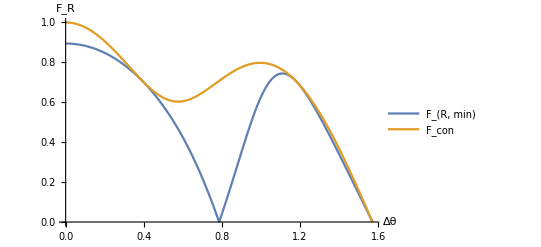

It may be confusing that the minimum relative fidelity is not 1 for Δθ = 0, however the input fidelity required to achieve the minimum at Δθ = 0 is also 0.

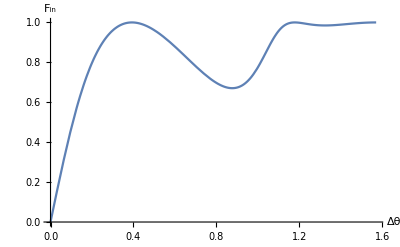

Note too that F_(R, min) and F_con coincide for certain values of Δθ, even when F_con ≠ 0.

We can find these values.

{{Δθ→(3 π)/8},{Δθ→(3 π)/8},{Δθ→π/8},{Δθ→π/8}}

```mathematica
"We can now plot F_(R, min) and F_con as functions of the channel parameter, Δθ."
"Minimum relative fidelity only goes to zero if Δθ is a multiple of π/4, as expected."
Plot[{relFidMin,Fcon},{Δθ,0,π/2},AxesLabel->{"Δθ","F_R"},PlotLegends->{"F_(R, min)","F_con"}]
"It may be confusing that the minimum relative fidelity is not 1 for Δθ = 0, however the input fidelity required to achieve the minimum at Δθ = 0 is also 0."
Plot[inFidForMinFR,{Δθ,0,π/2},AxesLabel->{"Δθ","F_in"}]
"Note too that F_(R, min) and F_con coincide for certain values of Δθ, even when F_con ≠ 0."
"We can find these values."
FullSimplify[Solve[{Fcon==relFidMin,Δθ>0,Δθ<Pi/2},Δθ]]
```

```mathematica
(*Function for the minimum relative fidelity with f > the required input fidelity to achieve Subscript[F, R,min](0)*)
FR[f_,Δθ_]:=Min[(√(1/f^2+Cos[4 Δθ] ((2-1/f^2) Cos[2 Δθ]-2 √(-1+1/f^2) Sin[2 Δθ])))/(√2),(√(1/f^2+Cos[4 Δθ] ((2-1/f^2) Cos[2 Δθ]+2 √(-1+1/f^2) Sin[2 Δθ])))/(√2)]
(*Function for the required input fidelity to achieve Subscript[F, R,min](0)*)
ReqInFid[Δθ_]:=(1-Cos[2 Δθ] Cos[4 Δθ])/(√2 Abs[Sin[Δθ]] √(2+Cos[2 Δθ]-Cos[6 Δθ]))
(*Function for Subscript[F, R,min](0)*)
MinRelFid[Δθ_]:=√((Cos[Δθ]+Cos[3 Δθ])^2/(2+2 Cos[2 Δθ]+Cos[4 Δθ]))
```

```mathematica
"We can show that the bound based on only the asymptotic value F_(R, min)(0) can be significantly looser than one based on F_(R, min)(f)."
ΔθVal=N[Pi/100];
"Bound based on F_(R, min)(f) versus bound based on always using F_(R, min)(0)."
boundsList=NestWhileList[{FR[#[[1]],ΔθVal]#[[1]],MinRelFid[ΔθVal]#[[2]]}&,{1,1},#[[1]]>ReqInFid[ΔθVal]&]
"Log of the ratio between the bounds"
Map[Log10[#[[2]]/#[[1]]]&,boundsList]
```

We can show that the bound based on only the asymptotic value F_(R, min)(0) can be significantly looser than one based on F_(R, min)(f).

Bound based on F_(R, min)(f) versus bound based on always using F_(R, min)(0).

{{1,1},{0.997536,0.893279},{0.992898,0.797948},{0.986765,0.71279},{0.979323,0.636721},{0.970677,0.56877},{0.960898,0.50807},{0.950044,0.453849},{0.938162,0.405413},{0.925297,0.362147},{0.911487,0.323499},{0.89677,0.288975},{0.881182,0.258135},{0.864759,0.230587},{0.847535,0.205978},{0.829545,0.183996},{0.810823,0.16436},{0.791405,0.146819},{0.771324,0.131151},{0.750617,0.117154},{0.729318,0.104652},{0.707465,0.093483},{0.685094,0.0835065},{0.662244,0.0745946},{0.638952,0.0666338},{0.615259,0.0595226},{0.591206,0.0531703},{0.566835,0.0474959},{0.54219,0.0424271},{0.517318,0.0378993},{0.492266,0.0338546},{0.467086,0.0302417},{0.441832,0.0270142},{0.416561,0.0241313},{0.391338,0.021556},{0.366231,0.0192555},{0.341317,0.0172005},{0.31668,0.0153649},{0.292418,0.0137251},{0.268641,0.0122604},{0.245478,0.0109519},{0.223077,0.00978314},{0.201615,0.00873908},{0.181296,0.00780644},{0.162356,0.00697333},{0.145058,0.00622913}}

Log of the ratio between the bounds

{0,-0.0479414,-0.09493,-0.141252,-0.186977,-0.232138,-0.276754,-0.320833,-0.36438,-0.407396,-0.449878,-0.491821,-0.533218,-0.57406,-0.614336,-0.654031,-0.69313,-0.731615,-0.769466,-0.80666,-0.843172,-0.878972,-0.91403,-0.948311,-0.981774,-1.01438,-1.04607,-1.0768,-1.10651,-1.13513,-1.16258,-1.18879,-1.21366,-1.2371,-1.25899,-1.2792,-1.29762,-1.31409,-1.32849,-1.34067,-1.35052,-1.35798,-1.36306,-1.36594,-1.36703,-1.36711}

Finally, we demonstrate that there exists an adaptive strategy that beats any non-adaptive strategy for certain values of Δθ.

We consider a 2-use protocol. The input for the first use is the state |0>. The Pauli-X operator is applied to the output and the result is the input for the second use.

Output fidelity

(√(5+Cos[4 Δθ]+Cos[8 Δθ]+Cos[12 Δθ]))/(2 √2)

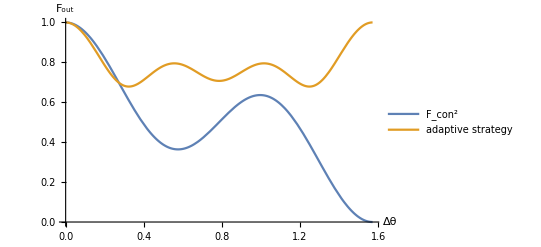

Since the adaptive strategy has a lower fidelity than F_con^2, for certain values of Δθ, adaptivity is shown to be of benefit for those values of Δθ.

```mathematica
"Finally, we demonstrate that there exists an adaptive strategy that beats any non-adaptive strategy for certain values of Δθ."
"We consider a 2-use protocol. The input for the first use is the state |0>. The Pauli-X operator is applied to the output and the result is the input for the second use."
adaptiveOut1=FullSimplify[2TraceFirstMode[ChoiC1.KroneckerProduct[PauliMatrix[1].(out1/.Subscript[θ, 1]->0).ConjugateTranspose[PauliMatrix[1]],IdentityMatrix[2]]],conds];
adaptiveOut2=FullSimplify[2TraceFirstMode[ChoiC2.KroneckerProduct[PauliMatrix[1].(out2/.Subscript[θ, 2]->0).ConjugateTranspose[PauliMatrix[1]],IdentityMatrix[2]]],conds];
"Output fidelity"
adaptiveFid=FullSimplify[Fidelity[adaptiveOut1,adaptiveOut2],conds]
Plot[{Fcon^2,adaptiveFid},{Δθ,0,Pi/2},AxesLabel->{"Δθ","F_out"},PlotLegends->{"F_con^2","adaptive strategy"}]
"Since the adaptive strategy has a lower fidelity than F_con^2, for certain values of Δθ, adaptivity is shown to be of benefit for those values of Δθ."
```